```mathematica
<<NCFPS`
SNC[x0,x1,x2];
```

# NCFPS

## Noncommutative Formal Power Series Commands for Mathematica

Lance Berlin, Luis A. Duffaut Espinosa,
W. Steven Gray

Maurício de Oliveira, J. William Helton, 
Benjamin C. Greenberg

August 30, 2021

## 0 Reserved Labels

### A

#### Description

For any η ∈ X^*, the coefficient, or coordinate, functions a_η^k are maps on formal series c∈ℝ^m⟨⟨X⟩⟩ yielding coeffcients

a_η^k(c):=⟨c_k,η⟩

where c_k=Σ_(η∈⟨X⟩)⟨c_i,η⟩η

This letter is reserved as the head for such functions and is used primarily with the functions , , , and .

#### Syntax

```mathematica
A[index,word]
```

index is the k^th element of c and word is the noncommutative word, η, which index a coordinate function a_η^k.
DO NOT include the series from which the function is to draw coefficients. Instead use the function MapCoordinateFunctions. This label exists for algebraic purposes.

#### Example

```mathematica
A[2,x0**x1]
```

A[2,x0**x1]

## 1 Elementary Commands

### CharacteristicSeries

#### Description

Given a subset L ⊆ X*, the characteristic series of L is the element in ℝ⟨⟨X⟩⟩ defined by char(L) =∑_(ν∈L) ν.

#### Syntax

```mathematica
CharacteristicSeries[list]
```

list is a list of words describing the language L.

#### Example

```mathematica
L={x0**x0,x1,x2**x1};
CharacteristicSeries[L]
```

x1+x0**x0+x2**x1

### FirstLetter

#### Description

Given η = x_i_1x_i_2⋯x_i_k ∈ X^*, the first letter of η is x_i_1 . The definition is extended linearly to series.

#### Syntax

```mathematica
FirstLetter[series]
```

series is noncommutative formal power series.

#### Example

```mathematica
FirstLetter[x1**x0+2x1**x0**x0]
```

3 x1

### ImproperPart

#### Description

The improper part of a series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is (c, ∅). The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ImproperPart[series]
```

series is a noncommutative formal power series.

#### Example

```mathematica
ImproperPart[1+x0+x0**x0+x0**x0**x0]
```

1

### LanguageFilter

#### Description

The polynomial c^* is the largest polynomial in c ∈ ℝ^ℓ⟨⟨X⟩⟩ such that supp(c^*)⊆L⊂X^*. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
LanguageFilter[c,L]
```

returns the largest polynomial in the noncommutative series c such that the support of that polynomial is a subset of the language L.

```mathematica
LanguageFilter[c,Y,X]
```

returns the largest polynomial in the noncommutative series c such that the support of that polynomial is a subset of the language Y^*⊂X^*, where Y and X are each noncommutative alphabets such that Y ⊂ X.

#### Example

```mathematica
c=2+x0-3x1**x0+4x0**x1**x0;
lang={1,x0,x1,x1**x0};
LanguageFilter[c,lang]
```

2+x0-3 x1**x0

```mathematica
c=2+x0+3x1**x0-4x2**x0;
y={x0,x1};
x={x0,x1,x2};
LanguageFilter[c,y,x]
```

2+x0+3 x1**x0

### NCDegree

#### Description

Given p ∈ ℝ^ℓ⟨X⟩, the degree of p is deg(p) = max{|η| : η ∈ supp(p)}. By definition, deg(0) = -∞. The partial degree with respect to x_i ∈ X is deg_x_i(p) = max{(|η|)_x_i : η ∈ supp(p)}. By definition, deg_x_i(0) = -∞. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
NCDegree[polynomial]
```

polynomial is a non-commutative formal polynomial.

```mathematica
NCDegree[polynomial,symbol]
```

symbol is a letter in a noncommutative alphabet.

#### Example

```mathematica
NCDegree[x1**x0**x0**x1+x1**x1**x1]
```

4

```mathematica
NCDegree[x1**x0**x0**x1+x1**x1**x1,x1]
```

3

### NCOrder

#### Description

Given c ∈ ℝ^ℓ⟨⟨X⟩⟩, the order of c is ord(c) = min{|η| : η ∈ supp(c)}. By definition, ord(0) = ∞. The partial order with respect to x_i ∈ X is ord_x_i(c) = min{(|η|)_x_i : η ∈ supp(c)}. By definition, ord_x_i(0) = ∞. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
NCOrder[series]
```

series is a noncommutative formal power series.

```mathematica
NCOrder[series,symbol]
```

symbol is a letter in a noncommutative alphabet.

#### Example

```mathematica
NCOrder[x1**x0**x0**x1+x1**x1**x1]
```

3

```mathematica
NCOrder[x1**x0**x0**x1+x1**x1**x1,x1]
```

2

### NCPrefix

#### Description

Given words η, ν ∈ X^*, the word η is a prefix of the word ην.

#### Syntax

```mathematica
NCPrefix[monomial,list]
```

monomial is a noncommutative monomial, and list is a list of noncommutative monomials.

#### Example

```mathematica
NCPrefix[x1**x0,{x1,x0**x1}]
```

{x1**x0**x1,x1**x0**x0**x1}

### ProperPart

#### Description

The proper part of a series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is c' = c - (c, ∅). The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ProperPart[series]
```

series is a noncommutative formal power series.

#### Example

```mathematica
ProperPart[1+x0+x0**x0+x0**x0**x0]
```

x0+x0**x0+x0**x0**x0

### ProperQ

#### Description

The proper part of a series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is c' = c − (c, ∅). The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ProperQ[series]
```

series is a noncommutative formal power series.

#### Example

```mathematica
ProperQ[1+x0+x0**x0+x0**x0**x0]
```

False

### RelativeDegree

#### Description

Suppose X = {x_0, x_1, … , x_m}. Any series c ∈ ℝ^ℓ⟨⟨X⟩⟩ can be written as c = c_N + c_F , where c_N := ∑_(k≥0) (c,x_0^k)x_0^k and c_F := c − c_N. The distinguished letter x_0 is called the drift letter. For each component series c_i ∈ ℝ⟨⟨X⟩⟩, i = 1, 2,…, ℓ, let r_i ≥ 1 be the largest integer such that supp(c_(i,F)) ⊆ x_0^(r_i-1)X^*. Then c_i has relative degree r_i if the linear word x_0^(r_i-1)x_j ∈ supp(c_i) for some j ∈ {0, 1,…,m}, otherwise it is not well defined. In addition, c has (vector) relative degree {r_1, r_2,…, r_ℓ} if the ℓ × m matrix

A = ((c_1,x_0^(r_1-1)x_1) | (c_1,x_0^(r_1-1)x_2) | ⋯ | (c_1,x_0^(r_1-1)x_m)
(c_2,x_0^(r_2-1)x_1) | (c_1,x_0^(r_2-1)x_2) | ⋯ | (c_1,x_0^(r_1-1)x_m)
⋮ | ⋮ | ⋱ | ⋮
(c_ℓ,x_0^(r_ℓ-1)x_1) | (c_ℓ,x_0^(r_ℓ-1)x_2) | ⋯ | (c_ℓ,x_0^(r_ℓ-1)x_m))

has full rank. Otherwise, c does not have relative degree. By far, the most common occurrence of this definition is for the case where ℓ = m. In which case, the condition on A is equivalent to det(A) ≠ 0.

#### Syntax

```mathematica
RelativeDegree[series,list,symbol]
```

series is a noncommutative formal power series in the alphabet defined by list. symbol is the drift letter.

#### Example

```mathematica
RelativeDegree[x0+x0**x1+x0**x0**x1+x0**x1**x0+x0**x1**x0**x1,{x0,x1},x0]
```

{2}

### RhoRightAugment

#### Description

Let (θ̃)_i^ρ denote the antipodal right-augmentation operator and X={x_0,x_1,…,x_m}. This mapping operates on coordinate functions (see ) according to

(θ̃)_i^ρ(a_η^k):=-(θ̃)_i(a_η^k)   ∀ i≠0
(θ̃)_0^ρ(a_η^k):=-(θ̃)_0(a_η^k)+∑_(r=1)^m a_∅^r(θ̃)_r(a_η^k)

See .

This operator acts as a derivation

(θ̃)_i^ρ(a_η_1^k_1⋯ a_η_s^k_s):=∑_(j=1)^s a_η_1^k_1⋯ (θ̃)_i^ρ(a_η_j^k_j)⋯ a_η_s^k_s

#### Syntax

```mathematica
RhoRightAugment[cfunc,ind,alph]
```

cfunc is a coordinate function of the type described in , ind is the index of the corresponding letter in the alphabet alph.

#### Example

```mathematica
X={x0,x1};
RhoRightAugment[A[1,x0**x1],0,X]
```

-A[1,x0**x1**x0]+A[1,1] A[1,x0**x1**x1]

### RightAugment

#### Description

Let (θ̃)_i denote the right-augmentation operator and X={x_0,x_1,…,x_m}. This endomorphism adds letters to the right of a specified coordinate function (see )

(θ̃)_i(a_η^k):=a_ηx_i^k
(θ̃)_i(1)=0

May need to overhaul to implement the following functionality:
For a word η:=x_i_1⋯ x_i_r and an arbitrary word ψ∈X^*

(θ̃)_η(a_η^k)=(θ̃)_i_r∘ ⋯ ∘(θ̃)_i_1(a_ψ^k)

This operator acts as a derivation

(θ̃)_i(a_η_1^k_1⋯ a_η_s^k_s):=∑_(j=1)^s a_η_1^k_1⋯ a_(η_j x_i)^k_j⋯ a_η_s^k_s

#### Syntax

```mathematica
RightAugment[cfunc,ind,alph]
```

cfunc is a coordinate function of the type described in , ind is the index of the corresponding letter in the alphabet alph.

#### Example

```mathematica
X={x0,x1};
RightAugment[A[1,x0**x1],0,X]
```

A[1,x0**x1**x0]

### Support

#### Description

Given c ∈ ℝ^ℓ⟨⟨X⟩⟩, the support of c is supp(c) = {η ∈ X^* : (c, η) ≠ 0}. The current implementation ℓ = 1.

#### Syntax

```mathematica
Support[series]
```

series is noncommutative formal power series.

#### Example

```mathematica
Support[x1**x0+2x1**x0**x0]
```

{x1**x0,x1**x0**x0}

### TruncateSeries

#### Description

A series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is truncated to a polynomial in ℝ^ℓ⟨X⟩ of degree n. The current implementation assumes m = ℓ = 1.

#### Syntax

```mathematica
TruncateSeries[series,integer]
```

series is a noncommutative formal power series, and integer is a nonnegative integer.

#### Example

```mathematica
TruncateSeries[1+x0+x0**x0+x0**x0**x0,2]
```

1+x0+x0**x0

### WordLength

#### Description

Given η ∈ X^*, the word length, |η|, is the number of symbols in η. The word length with respect to x_i ∈ X, (|η|)_x_i, is the number of symbols in η that match x_i.

#### Syntax

```mathematica
WordLength[list]
```

list is a list of monic noncommutative monomials.

```mathematica
WordLength[list,symbol]
```

symbol is a letter in X.

#### Example

```mathematica
WordLength[{x1**x0**x0**x1,1,x1**x1**x0}]
```

{4,0,3}

```mathematica
WordLength[{x1**x0**x0**x1,1,x1**x1**x0},x0]
```

{2,0,1}

## 2 Unitary Commands

### Antipode

#### Description

For a word η:=x_i_1⋯ x_i_r≠∅, the antipode S can be written

S(a_η^k)=(-1)^(r-1)(Θ̃)_η^ρ(a_∅^k)

where

(Θ̃)_η^ρ:=(θ̃)_i_r^ρ∘ ⋯ ∘(θ̃)_i_1^ρ

See .

#### Syntax

```mathematica
Antipode[cfunc,alph]
```

cfunc is a coordinate function of the type described in , alph is the alphabet for the context being operated in.

#### Example

```mathematica
X={x0,x1};
Antipode[A[1,x0**x1],X]
```

A[1,x1]^2-A[1,x0**x1]+A[1,1] A[1,x1**x1]

### CauchyInverse

#### Description

#### Syntax

#### Example

### CompositionInverse

#### Description

Calculates the compositional inverse of a series, c, such that

c ∘ c^-1 = δ

where

c ∘ δ = c   ∀ c ∈ ℝ⟨⟨X⟩⟩ .

The current version only supports the single-input, single-output case where c ∈ ℝ⟨⟨X⟩⟩ for X={x_0,x_1}.

#### Syntax

```mathematica
CompositionInverse[series, alphabet, degree]
```

series is a noncommutative formal power series, alphabet is a list of letters, degree is an integer that specifies the maximum degree of the resulting series.

#### Example

```mathematica
x = {x0, x1};
CompositionInverse[x0**x1 + 2 x1, x, 3]
```

-2 x1+3 x0**x1

### GlobalGrowthConstants

#### Description

A series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is said to be globally convergent if there exists real numbers K,M > 0 such that |(c, η)| ≤ KM^(|η|) for all η ∈ X^*, where |z| = max_i  |z_i| when z ∈ ℝ^ℓ, and |η| denotes the length of the word η. The smallest such constants are called the global growth constants. When possible, this command returns the minimal K,M (in this order) and plots log(|(c, η)|) versus word length, as well as the uniform bound log(M)|η| + log(K).

Assume there exists an expression such that |(c, η)| ≤ KM_0^((|η|)_x_0)M_1^((|η|)_x_1)⋯M_m^((|η|)_x_m)for all η ∈ X^* and X = {x_0, x_1, …, x_m}. When including a list alphabet, the command returns the minimal K,M_0,M_1,...,M_m (in this order) as well as showing a table of error values for the linearized fit of the form log(|(c, η)|) = log(K) + log(M_0)(|η|)_x_0+ log(M_1)(|η|)_x_1+ ⋯ + log(M_m)(|η|)_x_m

#### Syntax

```mathematica
GlobalGrowthConstants[series]
```

series is a noncommutative formal power series.

```mathematica
GlobalGrowthConstants[series,list]
```

list is a list containing an alphabet of letters.

#### Example

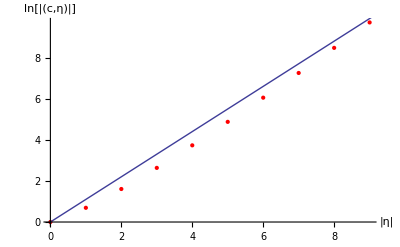

{1.,3.01008}

```mathematica
c = CharacteristicSeries[Table[CatalanNumber[n],{n,10}]*KleeneStar[{x0},9]];
GlobalGrowthConstants[c]
```

```mathematica
c=2+3x0+5x1+7x0**x0+9x0**x1+11x1**x0+12x0**x1**x0+15x0**x0**x0;
X={x0,x1};
GlobalGrowthConstants[c,X]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.6854 | 0.158152 | 4.33381 | 0.0074724
x0 | 0.617353 | 0.0790759 | 7.8071 | 0.000552573
x1 | 0.869613 | 0.15313 | 5.67893 | 0.00235791

{1.98457,1.85401,2.38599}

### HankelRank

#### Description

#### Syntax

#### Example

### IteratedIntegal

#### Description

#### Syntax

#### Example

### KleeneStar

#### Description

Given languages L, L̄ ⊆, define the product LL̄ = {ηη̄ ∈ X^* : η ∈ L, η̄ ∈ L̄}. The Kleene star of L is L^* = ∑_(k=0)^∞ L^k where L^0 denotes the empty word, and L^(k+1) = LL^k. In practice, only the first n + 1 terms of the summation can be computed, where n ≥0.

#### Syntax

```mathematica
KleeneStar[list,integer]
```

list is a list of monic monomials, and integer is a nonnegative integer.

#### Example

```mathematica
KleeneStar[{x0,x1},2]
```

{1,x0,x1,x0**x0,x0**x1,x1**x0,x1**x1}

### LeftShift

#### Description

Given any ξ ∈ X*, the corresponding left-shift operator on X* is defined as

ξ^-1 : X* → ℝ⟨X⟩ : η ↦ Piecewise[{{η', η=ξη'}, {0, otherwise.}}]

Note that in the second half of this definition, η is being mapped to the zero polynomial, i.e., p = 0, as opposed to the empty word ∅. So this operator is a mapping into ℝ⟨X⟩ and not into X*. For any c ∈ ℝ^ℓ⟨⟨X⟩⟩, this definition is extended linearly as

ξ^-1(c) = ∑_(η∈X^*) (c,η) ξ^-1(η) = (∑_)_(η∈X^*)(c,ξη)η.

The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
LeftShift[series,monomial]
```

series is a noncommutative formal power series, and monomial is a monic noncommutative monomial.

```mathematica
LeftShift[series,monomial,power]
```

power is a nonnegative integer.

#### Example

```mathematica
LeftShift[2x0**x1+x0**x1**x0+x1**x0**x0+x0**x0**x0,x0**x1]
```

2+x0

```mathematica
LeftShift[x0**x1**x0**x1**x0**x0,x0**x1,2]
```

x0**x0

```mathematica
LeftShift[x0**x1**x0**x1**x0**x0,x0**x1,0]
```

x0**x1**x0**x1**x0**x0

### LieRank

#### Description

#### Syntax

#### Example

### LocalGrowthConstants

#### Description

A series c ∈ ℝ^ℓ⟨⟨X⟩⟩ is said to be locally convergent if there exists real numbers K,M > 0 such that |(c, η)| ≤ KM^(|η|)|η|! for all η ∈ X^*, where |𝓏| = max_i  |𝓏_i| when 𝓏 ∈ ℝ^ℓ, and |η| denotes the length of the word η. The smallest such constants are called the local growth constants. When possible, this command returns the minimal K,M (in this order) and plots log(|(c,η)|/|η|!) versus word length, as well as the uniform bound log(M) |η| + log(K).

Assume there exists an expression such that |(c, η)| ≤ KM_0^((|η|)_x_0)M_1^((|η|)_x_1)⋯M_m^((|η|)_x_m)(|η|)_x_0!(|η|)_x_1!⋯(|η|)_x_m! for all η ∈ X^* and X = {x_0, x_1, …, x_m}. When including a list alphabet, the command returns the minimal K,M_0,M_1,...,M_m (in this order) as well as showing a table of error values for the linearized fit of the form log[|(c, η)|/((|η|)_x_0(|η|)_x_1⋯(|η|)_x_m)] = log(K) + log(M_0)(|η|)_x_0+ log(M_1)(|η|)_x_1+ ⋯ + log(M_m)(|η|)_x_m

#### Syntax

```mathematica
LocalGrowthConstants[series]
```

series is a noncommutative formal power series.

```mathematica
LocalGrowthConstants[series,list]
```

list is a list containing an alphabet of letters.

#### Example

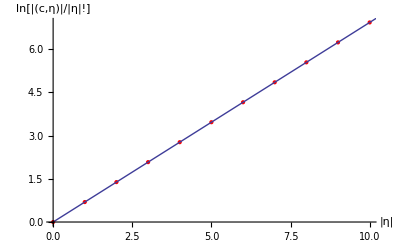

{1.,2.}

```mathematica
c = ShuffleInverse[1-2x0,10];
LocalGrowthConstants[c]
```

```mathematica
c=2+3x0+5x1+7x0**x0+9x0**x1+11x1**x0+12x0**x1**x0+15x0**x0**x0;
X={x0,x1};
LocalGrowthConstants[c,X]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.97384 | 0.339656 | 2.86713 | 0.0351121
x0 | -0.113217 | 0.169828 | -0.666658 | 0.534514
x1 | 1.00113 | 0.328871 | 3.04414 | 0.028615

{2.64809,0.892957,2.72136}

### NCExponential

#### Description

#### Syntax

#### Example

### NCLogarithm

#### Description

#### Syntax

#### Example

### RadiusOfConvergence

#### Description

#### Syntax

#### Example

### ShuffleInverse

#### Description

Let c ∈ ℝ^ℓ⟨⟨X⟩⟩ with (c, ∅) ≠ 0. The shuffle inverse of c is

c^(ш -1) = ((c, ∅) (1 - c'))^(ш -1) = (c, ∅)^-1∑_(k=0)^∞ (c')^(ш k).

The inverse is approximated to order n ≥ 0 if the upper bound of the summation above is n. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ShuffleInverse[series,integer]
```

series is a noncommutative formal power series, and integer is a nonnegative integer.

#### Example

```mathematica
c = 1+x0+x1;
cinv = NCExpand[ShuffleInverse[c,3]]
NCExpand[ShuffleProduct[c,cinv]]
```

1-x0-x1+2 x0**x0+2 x0**x1+2 x1**x0+2 x1**x1-6 x0**x0**x0-6 x0**x0**x1-6 x0**x1**x0-6 x0**x1**x1-6 x1**x0**x0-6 x1**x0**x1-6 x1**x1**x0-6 x1**x1**x1

1-24 x0**x0**x0**x0-24 x0**x0**x0**x1-24 x0**x0**x1**x0-24 x0**x0**x1**x1-24 x0**x1**x0**x0-24 x0**x1**x0**x1-24 x0**x1**x1**x0-24 x0**x1**x1**x1-24 x1**x0**x0**x0-24 x1**x0**x0**x1-24 x1**x0**x1**x0-24 x1**x0**x1**x1-24 x1**x1**x0**x0-24 x1**x1**x0**x1-24 x1**x1**x1**x0-24 x1**x1**x1**x1

## 3 Binary Commands

### CompositionProduct

#### Description

Suppose X = {x_0, x_1,…, x_m}, X̃ = {(x̃)_0, (x̃)_1, . . . , (x̃)_(m̃)}, c ∈ ℝ^(ℓ̃)⟨⟨X̃⟩⟩ and d ∈ ℝ^(m̃)⟨⟨X⟩⟩. Define the family of mappings

D_((x̃)_i) : ℝ⟨⟨X⟩⟩ → ℝ⟨⟨X⟩⟩ : ℯ ↦ x_0(d_i ш ℯ),

i = 0, 1,…, m̃ with d_0 = 1. Assume D_∅ is the identity map on ℝ⟨⟨X⟩⟩ and compose these operators in the obvious way so that D_((x̃)_i(x̃)_j) =: D_((x̃)_i)D_((x̃)_j). The composition of a word η ∈ X̃ and d is defined as

η̃ ◦ d = ((x̃)_i_k(x̃)_(i_(k-1))⋯(x̃)_i_1) ◦ d = D_((x̃)_i_k)D_((x̃)_(i_(k-1)))⋯D_((x̃)_i_1)(1) = D_(η̃)(1).

In which case, the composition product of c and d is

c ◦ d = ∑_(η̃∈X̃⋆) (c,η̃)η̃ ◦ d.

The composition power is defined as

c^(◦i) = c ◦ c ◦ ⋯ ◦ c ,

where c appears i times and c^(◦0) := 1.

The current implementation assumes X̃ = X and ℓ̃ = 1.

#### Syntax

```mathematica
CompositionProduct[series,list1,list2]
```

series is a noncommutative formal power series, list1 is a list of noncommutative formal power series, and list2 is a list of symbols defining an alphabet.

```mathematica
CompositionProduct[series,list2,power]
```

power is a nonnegative integer.

#### Example

```mathematica
X = {x0,x1,x2};
c = x1**x2;
d = {x0+2x1,x2};
CompositionProduct[c,d,X]
```

2 x0**x0**x0**x2+2 x0**x0**x1**x2+x0**x0**x2**x0+2 x0**x0**x2**x1+2 x0**x1**x0**x2

```mathematica
CompositionProduct[x0**x1,{x0,x1},2]
```

x0**x0**x0**x1

### FeedbackProduct

#### Description

#### Syntax

#### Example

### LieBracket

#### Description

#### Syntax

#### Example

### MapCoordinateFunctions

#### Description

This function takes an expression of coordinate functions and applies them to a noncommutative formal power series.

#### Syntax

```mathematica
MapCoordinateFunctions[cexp,series]
```

cexp is an expression of coordinate functions (see ), series is any noncommutative formal power series.

NOTE: It is very important that cexp does not contain any coordinate functions of words whose lengths are greater than the degree of series. This is because words which are not encountered in series are taken to have coefficients of 0. If series has been truncated such that NCDegree[series] evaluates to n and cexp contains a coordinate function A[word] such that WordLength[word]>n is True, then a cancellation of nonzero coefficients will occur. It is, however, safe for series to be of a greater degree than the largest word of any coordinte function in cexp.

#### Example

```mathematica
c=2+x0-x1**x0;
MapCoordinateFunctions[A[1,1]A[1,x1**x0]+A[1,x1],c]
```

-2

### ModifiedCompositionProduct

#### Description

Suppose X = {x_0, x_1,…, x_m}, X̃ = {(x̃)_0, (x̃)_1, . . . , (x̃)_(m̃)}, c ∈ ℝ^(ℓ̃)⟨⟨X̃⟩⟩ and d ∈ ℝ^(m̃)⟨⟨X⟩⟩. Define the family of mappings

(D̃)_((x̃)_i) : ℝ⟨⟨X⟩⟩ → ℝ⟨⟨X⟩⟩ : ℯ ↦ x_iℯ + x_0(d_i ш ℯ),

i = 0, 1,…, m̃ with d_0 := 0. Assume (D̃)_∅ is the identity map on ℝ⟨⟨X⟩⟩ and compose these operators in the obvious way so that (D̃)_((x̃)_i(x̃)_j) =: (D̃)_((x̃)_i)(D̃)_((x̃)_j). The composition of a word η̃ ∈ X̃ and d is defined as

η̃ OverTilde[◦] d = ((x̃)_i_k(x̃)_(i_(k-1))⋯(x̃)_i_1) OverTilde[◦] d = (D̃)_((x̃)_i_k)(D̃)_((x̃)_(i_(k-1)))⋯(D̃)_((x̃)_i_1)(1) = (D̃)_(η̃)(1).

In which case, the composition product of c and d is

c OverTilde[◦] d = ∑_(η̃∈X̃⋆) (c,η̃)η̃ OverTilde[◦] d.

The modified composition power is defined as

c^(OverTilde[◦]i) = c OverTilde[◦] c OverTilde[◦] ⋯ OverTilde[◦] c ,

where c appears i times and c^(OverTilde[◦]0) := 1.

The current implementation assumes X̃ = X and ℓ̃ = 1.

#### Syntax

```mathematica
ModifiedCompositionProduct[series,list1,list2]
```

series is a noncommutative formal power series, list1 is a list of noncommutatie formal power series, and list2 is a list of symbols defining an alphabet.

```mathematica
ModifiedCompositionProduct[series,list2,power]
```

power is a nonnegative integer.

#### Example

```mathematica
X = {x0,x1,x2};
c = x1**x2;
d = {x0+2x1,x2};
ModifiedCompositionProduct[c,d,X]
```

x1**x2+x0**x0**x2+2 x0**x1**x2+x0**x2**x0+2 x0**x2**x1+x1**x0**x2+2 x0**x0**x0**x2+2 x0**x0**x1**x2+x0**x0**x2**x0+2 x0**x0**x2**x1+2 x0**x1**x0**x2

```mathematica
ModifiedCompositionProduct[x0**x1,{x0,x1},2]
```

x0**x1+x0**x0**x0**x1

### ScalarProduct

#### Description

Given c,d ∈ ℝ^ℓ⟨⟨X⟩⟩, the scalar product is

(c, d) = ∑_(η=X*) ∑_(i=1)^ℓ (c_i,η)(d_i,η).

Of course for many series this sum diverges. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ScalarProduct[series1,series2]
```

series1 and series2 are noncommutative formal power series.

#### Example

```mathematica
ScalarProduct[x0**x1 + 3 x0**x0, x1**x1**x0 + 2 x0**x1]
```

2

### ShuffleProduct

#### Description

The shuffle product of two words η = x_jη', ξ = x_kξ' ∈ X^* is defined iteratively as

η ш ξ = (x_jη') ш (x_kξ') = x_j(η'ш ξ) + x_k(η ш ξ')

with ξ ш ∅ = ∅ ш ξ = ξ. The definition of the shuffle product is extended linearly to any two series c,d ∈ ℝ⟨⟨X⟩⟩ by letting

c ш d = ∑_(η,ξ∈X^*) (c,η)(d,ξ)η ш ξ.

Given two series c,d ∈ ℝ^ℓ⟨⟨X⟩⟩ the shuffle product c ш d is defined componentwise, i.e., the i-th component series of c ш d is (c ш d)_i = c_i ш d_i, where 1 ≤ i ≤ ℓ. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
ShuffleProduct[series1,series2]
```

series1 and series2 are noncommutative formal power series.

#### Example

```mathematica
NCExpand[ShuffleProduct[2x0**x1,x0+x1]]
```

4 x0**x0**x1+2 x0**x1**x0+4 x0**x1**x1+2 x1**x0**x1

### UltraMetricDistance

#### Description

An ultrametic on ℝ^ℓ⟨⟨X⟩⟩ is a mapping of the form

dist : ℝ^ℓ⟨⟨X⟩⟩ × ℝ^ℓ⟨⟨X⟩⟩ → ℝ : (c, d) ↦ σ^(ord(c-d))

where σ such that 0 < σ < 1. The current implementation assumes ℓ = 1.

#### Syntax

```mathematica
UltrameticDistance[series1,series2,real]
```

series1 and series2 are noncommutative formal power series, and real is a real number strictly between 0 and 1.

#### Example

```mathematica
UltrametricDistance[x0+x0**x1**x1+x1**x0**x0,x0+x0**x0+x0**x0**x0,0.5]
```

0.25

## 4 Other Commands

### RealizationToSeries

#### Description

Let G = {g_0, g_1,…, g_m} be a set of smooth ℝ^n-vector fields defined on a neighborhood W of z_0 ∈ ℝ^n. g_0 is taken as the drift vector field. Let h be a smooth ℝ^ℓ-valued function on W. The generating series of the realization (G, h, z_0) is c ∈ ℝ^ℓ⟨⟨X⟩⟩, where X = {x_0, x_1,…, x_m} and

(c, η) = L_g_i_1⋯L_g_i_kh(z_0), η = x_i_k⋯x_i_1 ∈ X^*

with L_g_i : h ↦ ∂h/∂z · g_i and L_∅h = h.

#### Syntax

```mathematica
RealizationToSeries[list1,function,list2,list3,integer]
```

list1 is a list of m+1 mappings from ℝ^n to ℝ^n, function is a mapping from ℝ^n to ℝ^ℓ, list2 is a list of n real numbers describing an initial condition, and list3 is the m+1 letter alphabet for the generating series c. The output series c is truncated to degree integer. The current implementation assumes ℓ = 1.

#### Example

```mathematica
g0[z1_,z2_,z3_,z4_]:={z1 z2-z1^3,z1,-z3,z1^2+z2}
g1[z1_,z2_,z3_,z4_]:={0,2+2 z3,1,0}
h[z1_,z2_,z3_,z4_]:=z4
z0:={0,0,0,0}
X={x0,x1};
RealizationToSeries[{g0,g1},h,z0,X,5]
```

2 x0**x1+2 x0**x1**x1-2 x0**x1**x0**x1+2 x0**x1**x0**x0**x1